# Nonstationary simulation, large model

```mathematica
<<NilssonLab`MetabolicNetwork`
```

```mathematica
<<NilssonLab`ExtremePathways`
<<NilssonLab`IsotopeDistributions`
<<NilssonLab`AtomMap`
<<NilssonLab`EMUTracing`
```

```mathematica
<<NilssonLab`Visualization`
```

```mathematica
OpenDBConnection[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\code\nonstationary-mid-sim

```mathematica
resultDirectory="C:\\Users\\rolnil\\OneDrive - KI.SE\\Lab common\\projects\\reverse-engineering-deniz\\reverse-engineering\\Data\\simulation\\large-model";
```

```mathematica
$HistoryLength=0;
```

## Define network model

### Network from database

```mathematica
net=NetworkFromDB["central-metabolism-5"]
```

NetworkFromDB::nonintstoch: Coefficient Cellgrowth_Alberts_no_lipids in reaction -0.017 was rounded.

NetworkFromDB::nonintstoch: Coefficient Cellgrowth_Alberts_no_lipids in reaction -0.002 was rounded.

NetworkFromDB::nonintstoch: Coefficient Cellgrowth_Alberts_no_lipids in reaction -0.005 was rounded.

General::stop: Further output of NetworkFromDB::nonintstoch will be suppressed during this calculation.

<MetabolicNetwork, 554 reactions>

```mathematica
Length[Metabolites[net]]
```

477

Stochiometry matrix (metabolites x reactions) for the reversible network

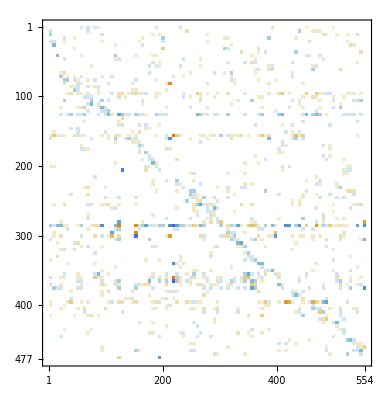

```mathematica
MatrixPlot[Stoichiometry[net]]
```

```mathematica
Union[NonZeroElements[Stoichiometry[net]]]
```

{-8,-5,-4,-3,-2,-1,1,2,3,4}

#### Generate boundary network

```mathematica
bnet=BoundaryNetwork[net]
```

<BoundaryNetwork, 62 boundary fluxes>

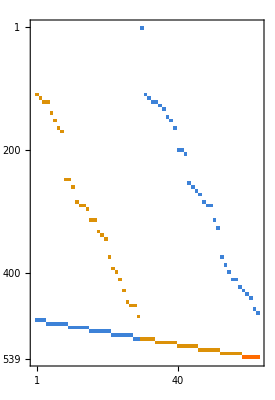

```mathematica
Stoichiometry[bnet]//MatrixPlot
```

```mathematica
BoundaryFluxNames[bnet]
```

{ala-L_IN,arg-L_IN,asn-L_IN,asp-L_IN,chol_IN,citr-L_IN,creat_IN,cys-L_IN,glc-D_IN,gln-L_IN,gly_IN,h2o_IN,h_IN,hdca_IN,his-L_IN,ile-L_IN,inost_IN,leu-L_IN,lys-L_IN,met-L_IN,o2_IN,phe-L_IN,pi_IN,pro-L_IN,ser-L_IN,thr-L_IN,trp-L_IN,tyr-L_IN,val-L_IN,1c_OUT,ala-L_OUT,arg-L_OUT,asn-L_OUT,asp-L_OUT,bhb_OUT,biomass_OUT,chsterol_OUT,co2_OUT,crtn_OUT,dna_OUT,dopa_OUT,energy_OUT,glu-L_OUT,gly_OUT,glycogen_OUT,gthrd_OUT,h2o_OUT,h_OUT,hdca_OUT,inost_OUT,lac-L_OUT,nh4_OUT,oxa_OUT,pi_OUT,pro-L_OUT,protein_OUT,rna_OUT,ser-L_OUT,sprm_OUT,taur_OUT,urate_OUT,urea_OUT}

## Choose a flux vector

### Ratio-balanced flux vector

```mathematica
<<NilssonLab`GAMSFluxEstimation`
```

Use the “balanced ratios” vector as the “true” flux state

```mathematica
trueFlux=ImportGAMSFluxes[Directory[],"balanced-ratios",net,EMUFluxMap[net]]
```

<FluxState, 554 reactions, 62 b. exch>

## Atom map

### Define atom map

All atom transitions for reactions in model

```mathematica
atomMap=RemoveUnreachable[net,AtomMapsFromDB[net,{"C"}]];
```

Renumber for use with INCA

```mathematica
atomMap=RenumberAtoms[atomMap];
```

Consistency check, ensure that there are no broken paths on the atom level

```mathematica
CheckAtomMap[atomMap]
```

{}

```mathematica
AtomList[atomMap]//Length
```

2693

```mathematica
Total[Length/@EductList/@atomMap]
```

4447

Cretate boundary atom maps (uptake / release)

```mathematica
bmap=BoundaryAtomMaps[net,atomMap];
bmap//Length
```

62

## Define measured EMUs

```mathematica
targets=MetaboliteEMUs[atomMap];
targets//Length
```

404

Total # of measurements

```mathematica
Total[Flatten[Dimensions/@targets+1]]
```

3097

```mathematica
Total[Flatten[Dimensions/@First/@GatherBy[targets,MetaboliteID[First[#]]&]]+1]
```

2538

## Symmetry

### Generate equivalent EMUs

Check symmetry from atom map (this does not account for prochirality! use only as a guide)

```mathematica
symmetry=GetSymmetryMap[atomMap]
```

{34hpp→{{1,2},{3,4}},acetone→{{1,2}},betald→{{1,2,3}},chol→{{1,2,3}},cholp→{{1,2,3}},dmgly→{{1,2}},fum→{{1,2},{3,4}},glyb→{{1,2,3}},gthox→{{1,2},{3,4},{5,6},{7,8},{9,10},{11,12},{13,14},{15,16},{17,18},{19,20}},inost→{{1,2,3,4,5,6}},oxa→{{1,2}},phe-L→{{2,3},{4,5}},pmtcrn→{{2,3,4}},ptrc→{{1,2},{3,4}},sprm→{{1,2},{3,4},{5,6},{7,8},{9,10}},sql→{{5,6},{7,8},{9,10},{11,12},{13,14},{15,16},{17,18},{19,20},{21,22},{23,24},{25,26},{27,28},{29,30},{1,2,3,4}},succ→{{1,2},{3,4}},tyr-L→{{1,2},{3,4}}}

Not all atoms above are reachable from substrates, e.g. the THF moiety

Dumpsave for use with script

```mathematica
(*DumpSave["symmetry.mx", symmetry];*)
```

```mathematica
Length[symmetry]
```

18

## EMU model

### Run the EMU decomposition algorithm

Find EMU reactions (this takes some time)

```mathematica
emuReactions=EMUAlgorithm[net,atomMap,bmap,{"C"},targets,symmetry];
Length[emuReactions]
```

11981

```mathematica
emuReactionNames=EMUFluxMap[net,"reactions"];
```

```mathematica
Length[emuReactionNames]
```

819

```mathematica
RandomSample[emuReactions,10]
```

{EMUReaction[93,<prpp_c{(123)}>,<amp_c{(146)}>,1],EMUReaction[502,<5aizc_c{(1356)}>,<25aics_c{(2589)}>,1],EMUReaction[472,<1pyr5c_c{(4)}>,<pro-L_c{(4)}>,1],EMUReaction[655,<2mop_m{(14)}>,<3aib-D_m{(14)}>,1],EMUReaction[291,<atp_c{(7a)}>,<adp_c{(7a)}>,1],EMUReaction[66,<gam6p_c{(6)}>,<acgam6p_c{(8)}>,1],EMUReaction[657,<dump_c{(45)}>,<dcmp_c{(45)}>,1],EMUReaction[97,<imp_c{(23589)}>,<dcamp_c{(348bc)}>,1],EMUReaction[107,<akg_m{(13)}>,<glu-L_m{(13)}>,1],EMUReaction[658,<atp_c{(3589)}>,<adp_c{(3589)}>,1]}

Number of EMUs

```mathematica
emus=Union[Cases[emuReactions,EMUReaction[_,_,e_EMU,_]->e]];
emus//Length
```

4803

All targets are included

```mathematica
Complement[targets,emus]
```

{}

Total number of variables (MI fractions)

```mathematica
Total[Map[(Times@@#&),(Dimensions/@emus)+1]]
```

17106

Dump save

```mathematica
(*DumpSave["emuReactions_emus_renumbered.mx",{emuReactions,emus}];*)
```

### Quick load

```mathematica
<<"emuReactions_emus_renumbered.mx";
```

Get::noopen: Cannot open emuReactions_emus_renumbered.mx.

### Generate equation systems

```mathematica
emuEq=EMUSystem[emuReactions,NumberOfFluxes[EMUFluxMap[net]]];
```

```mathematica
TableForm[emuEq,TableHeadings->Automatic]
```

1 | <EMUEquation (1), 1878 internals, 127 substrates, 0 condensations >
2 | <EMUEquation (2), 1524 internals, 118 substrates, 32 condensations >
3 | <EMUEquation (3), 478 internals, 40 substrates, 19 condensations >
4 | <EMUEquation (4), 357 internals, 26 substrates, 23 condensations >
5 | <EMUEquation (5), 237 internals, 13 substrates, 16 condensations >
6 | <EMUEquation (6), 101 internals, 10 substrates, 14 condensations >
7 | <EMUEquation (7), 11 internals, 1 substrates, 5 condensations >
8 | <EMUEquation (8), 37 internals, 3 substrates, 5 condensations >
9 | <EMUEquation (9), 45 internals, 2 substrates, 11 condensations >
10 | <EMUEquation (10), 58 internals, 2 substrates, 20 condensations >
11 | <EMUEquation (11), 9 internals, 1 substrates, 6 condensations >
12 | <EMUEquation (12), 12 internals, 1 substrates, 2 condensations >
13 | <EMUEquation (13), 4 internals, 0 substrates, 3 condensations >
14 | <EMUEquation (14), 17 internals, 1 substrates, 7 condensations >
15 | <EMUEquation (15), 4 internals, 0 substrates, 4 condensations >
16 | <EMUEquation (16), 6 internals, 1 substrates, 1 condensations >
17 | <EMUEquation (17), 1 internals, 0 substrates, 1 condensations >
18 | <EMUEquation (20), 1 internals, 0 substrates, 1 condensations >
19 | <EMUEquation (27), 15 internals, 0 substrates, 2 condensations >
20 | <EMUEquation (29), 5 internals, 0 substrates, 2 condensations >
21 | <EMUEquation (30), 3 internals, 0 substrates, 1 condensations >

## Specify input isotopomers (tracers)

```mathematica
substrates=Cases[MetaboliteEMUs[bmap],EMU[Metabolite[_,"Input",_],__]]
```

{<ala-L_i{(123)}>,<arg-L_i{(123456)}>,<asn-L_i{(1234)}>,<asp-L_i{(1234)}>,<chol_i{(12345)}>,<citr-L_i{(123456)}>,<creat_i{(1234)}>,<cys-L_i{(123)}>,<glc-D_i{(123456)}>,<gln-L_i{(12345)}>,<gly_i{(12)}>,<hdca_i{(123456789abcdefg)}>,<his-L_i{(123456)}>,<ile-L_i{(123456)}>,<inost_i{(123456)}>,<leu-L_i{(123456)}>,<lys-L_i{(123456)}>,<met-L_i{(12345)}>,<phe-L_i{(123456789)}>,<pro-L_i{(12345)}>,<ser-L_i{(123)}>,<thr-L_i{(1234)}>,<trp-L_i{(123456789ab)}>,<tyr-L_i{(123456789)}>,<val-L_i{(12345)}>}

```mathematica
deepLabelingMetIDs={"ala-L","arg-L","asn-L","asp-L","cys-L","glc-D","gln-L","gly","his-L","ile-L","leu-L","lys-L","met-L","phe-L","pro-L","ser-L","thr-L","trp-L","tyr-L","val-L"};
```

### Specify substrate isotopomer distributions for each simulation

List the input metabolites that have atom information; for these the isotope distributions must be specified.

No natural 13C, tracer purity = 1

```mathematica
substrateDist=Join[
(* single substrates labeled *)
Table[
substrates/.{
e:EMU[met,__]:>Rule[met,EmpiricalIsotopomerDistribution[{{{Table[1,EMUSize[e]]},1.0}}]],
e:EMU[m_Metabolite,__]:>
Rule[m,EmpiricalIsotopomerDistribution[{{{Table[0,EMUSize[e]]},1.0}}]]},
{met,Metabolite/@substrates}],
{(* deep labeling *)
substrates/.{
e:EMU[met:Metabolite[Alternatives@@deepLabelingMetIDs,__],_]:>Rule[met,EmpiricalIsotopomerDistribution[{{{Table[1,EMUSize[e]]},1.0}}]],
e:EMU[m_Metabolite,__]:>
Rule[m,EmpiricalIsotopomerDistribution[{{{Table[0,EMUSize[e]]},1.0}}]]},
(* all substrates labeled *)
substrates/.{
e:EMU[met_Metabolite,_]:>Rule[met,EmpiricalIsotopomerDistribution[{{{Table[1,EMUSize[e]]},1.0}}]]}}];
```

```mathematica
Length[substrateDist]
```

27

```mathematica
simulationNames=Join[MetaboliteID/@Metabolite/@substrates,{"deep labeling", "full labeling"}]
```

{ala-L,arg-L,asn-L,asp-L,chol,citr-L,creat,cys-L,glc-D,gln-L,gly,hdca,his-L,ile-L,inost,leu-L,lys-L,met-L,phe-L,pro-L,ser-L,thr-L,trp-L,tyr-L,val-L,deep labeling,full labeling}

### Calculate substrate EMU MIDs

TODO: handle case where inputs have symmetry. MarginalizeToMID does not deal with these correctly.

```mathematica
allSubstrates=Flatten[SubstrateEMUs/@emuEq];
```

Mass isotopomer distribution of an EMU for a metabolite with given isotopomer distribution.
For symmetric molecules that yield equivalence classes like <chol_i{(1)|(2)|(3)}>,
the isotopomer probability must be the same for any permutation of the atoms in the equivalence class,
e.g. p(100) = p(010) = p(001). The MID for the equivalence class is the same as the MID for each member, which are all equal.

```mathematica
EMUMassIsotopomerDistribution[e_EMU,isoDist_]:=
Block[{a,ml},
(* arbitrarily pick first member of equiv. class *)
a=First[AtomNumbers[e]];
(* list of masses of the EMU *)
ml=Tuples[Map[Range[0,Length[#]]&,a]];
Table[
PDF[MarginalizeToMID[FragmentIsotopomerDistribution[isoDist,a]],x],
{x,ml}]]
```

```mathematica
irList=Table[
Table[
Rule[e,EMUMassIsotopomerDistribution[e,Metabolite[e]/.dist]],
{e,Flatten[SubstrateEMUs/@emuEq]}],
{dist,substrateDist}];
```

Check that all substrate EMUs sum to 1

```mathematica
Table[
Cases[Total/@Last/@ir,t_/;t>1],{ir,irList}]
```

{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

## Simulate steady-state isotopomer data

### Simulate EMUs

One simulation for each substrate list

```mathematica
emuSol=Table[
EMUSimulate[emuEq,ir,EMUFluxMap[net][trueFlux]],
{ir,irList}];
```

```mathematica
Length[emuSol]
```

27

Enrichment distribution

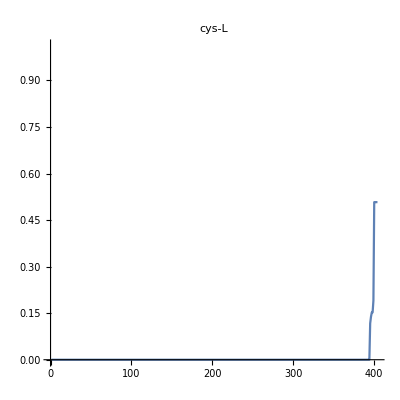
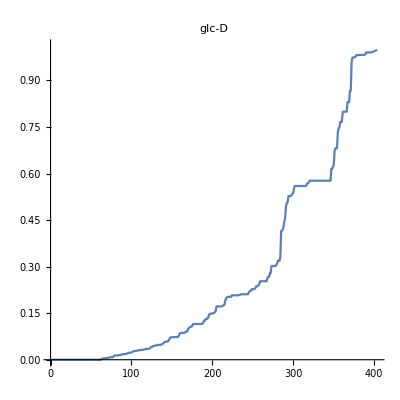
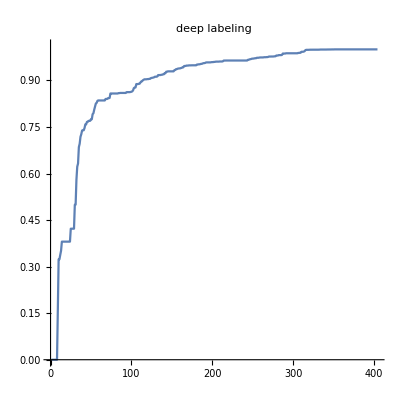
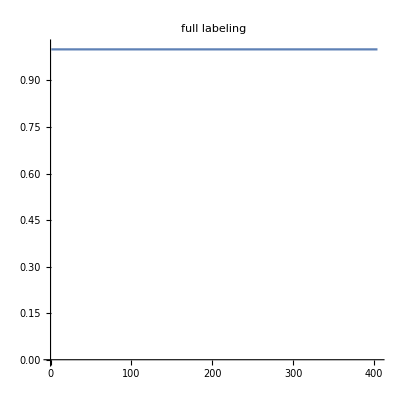

```mathematica
Table[
ListPlot[
Sort[MIDEnrichment/@emuSol⟦i⟧/@targets],
PlotRange->{0,1.01},Joined->True,AspectRatio->1,PlotLabel->simulationNames⟦i⟧],
{i,{8,9,26,27}}]
```

```mathematica
Cases[targets,e_/;MIDEnrichment[emuSol⟦8⟧[e]]>0.001]
```

{<3sala_c{(123)}>,<cys-L_c{(123)}>,<glucys_c{(12345678)}>,<gthox_c{(123456789abcdefghijk)}>,<gthrd_c{(123456789a)}>,<hyptaur_c{(12)}>,<Lcyst_c{(123)}>,<lgt-S_c{(123456789abcd)}>,<Sfglutth_c{(123456789ab)}>,<taur_c{(12)}>}

```mathematica
Cases[MIDEnrichment/@emuSol⟦8⟧/@targets,e_/;e>0.001]
```

{0.507793,0.507793,0.190422,0.152338,0.152338,0.507793,0.507793,0.117183,0.138489,0.507793}

### Export stationary MIDs

Single matrix, each column is one simulation

```mathematica
(*Export[
FileNameJoin[{resultDirectory,"steady-state.tsv"}],
Block[{mi,met},
met=Flatten[Table[MetaboliteShortName[Metabolite[e]],{e,targets},{i,0,EMUSize[e]}]];
mi=Flatten[Table[Range[0,EMUSize[e]],{e,targets}]];
ArrayFlatten[
{{{{"Metabolite","MI"}},{simulationNames}},
{Transpose[{met,mi}],Transpose[Table[Flatten[emuSol⟦i⟧/@targets],{i,Length[simulationNames]}]]}}]]]*)
```

C:\Users\rolnil\OneDrive - KI.SE\Lab common\projects\reverse-engineering-deniz\reverse-engineering\Data\simulation\large-model\steady-state.tsv

## Nonstationary simulation

### Parameters

Here, all MI fractions are time-dependent variables, and each internal EMU is associate with a differential equation over time rather than an algebraic equation. The condensations are the same, but also time dependent.

In tensor form, the steady state equation is A v X + B v Y + C v Z - D v X = 0  <--> (A-D) v X = - B v Y - C v Z
The nonstationary version is 
T * dX/dt = A v X(t) + B b Y + C v Z(t) - D v X(t)
where T is a diagnonal matrix of concentrations for each metabolite (same for all EMUs from that metabolite)

Define concentrations for each metabolite

```mathematica
metaboliteConc=Thread[Metabolites[net]->1.0];
```

```mathematica
variables=Table[
x[e,j],
{eq,emuEq},{e,InternalEMUs[eq]},{j,0,EMUSize[First[InternalEMUs[eq]]]}];
```

We will need an initial MID state. Here we take the unlabeled state, so that x[e, j] is the unit vector

```mathematica
initial=Table[
x[e,j][0]==If[j==0,1,0],
{eq,emuEq},{e,InternalEMUs[eq]},{j,0,EMUSize[First[InternalEMUs[eq]]]}];
```

```mathematica
tFinal=2000.0;
```

### Generate equation systems

Substrate distributions are hardcoded into the differential equations

```mathematica
emuDiffEqn=Block[{v,c},
v=EMUFluxMap[net][trueFlux];
c=Map[Metabolite,InternalEMUs/@emuEq,{2}]/.metaboliteConc;
Table[
EMUDiffEquation[emuEq,x,t,irList⟦i⟧,v,c],
{i,Length[simulationNames]}]];
```

```mathematica
Dimensions/@emuDiffEqn⟦8⟧
```

{{1878,2},{1524,3},{478,4},{357,5},{237,6},{101,7},{11,8},{37,9},{45,10},{58,11},{9,12},{12,13},{4,14},{17,15},{4,16},{6,17},{1,18},{1,21},{15,28},{5,30},{3,31}}

### Simulate systems

Simulation with NDSolve. Skip the cysteine case

```mathematica
sol=MemoryConstrained[
Table[
If[k==8,{},
variables/.First[
NDSolve[
Join[Flatten[emuDiffEqn⟦k⟧],Flatten[initial]],
Flatten[variables],{t,0,tFinal}]]],
{k,Length[simulationNames]}],
6*10^9];
```

```mathematica
Length[sol]
```

27

```mathematica
Clear[sol]
```

The cysteine simulation -- requires about 8Gb memory and runs forever. Limit by MaxSteps?

```mathematica
sol=Table[{},Length[simulationNames]];
```

```mathematica
sol⟦8⟧=MemoryConstrained[
With[{k=8},
variables/.First[
NDSolve[
Join[Flatten[emuDiffEqn⟦k⟧],Flatten[initial]],
Flatten[variables],{t,0,tFinal},
PrecisionGoal->10^-4,AccuracyGoal->10^-4]]],
9*10^9];
```

$Aborted

```mathematica
Dimensions/@sol⟦8⟧
```

$Aborted

### Plot solutions

```mathematica
functionIndex=Join@@Table[Position[variables,x[e,EMUSize[e]]],{e,targets}];
```

#### All targets

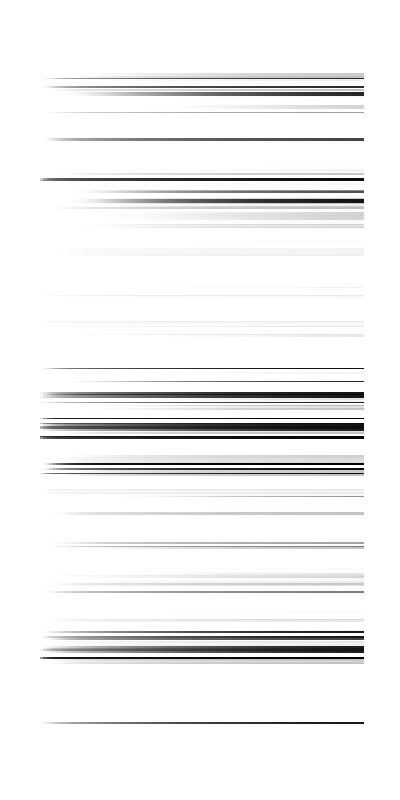

```mathematica
Block[{k=9,ix=functionIndex,fl,vl},
fl=Extract[sol⟦k⟧,ix];
vl=Extract[variables,ix];
ArrayPlot[
Table[f[t],{f,fl},{t,0,100,1}],
AspectRatio->2]]
```

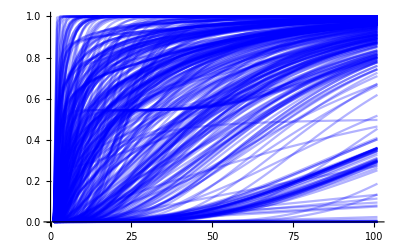

```mathematica
Block[{k=27,ix=functionIndex,fl,vl},
fl=Extract[sol⟦k⟧,ix];
vl=Extract[variables,ix];
ListPlot[
Table[f[t],{f,fl},{t,0,100,1}],
PlotRange->{0,1},Joined->True,PlotStyle->Directive[Blue,Opacity[0.3]]]]
```

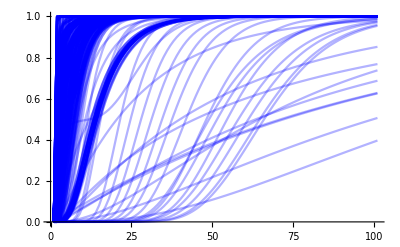

```mathematica
Block[{k=27,ix=functionIndex,fl,vl},
fl=Extract[sol⟦k⟧,ix];
vl=Extract[variables,ix];
ListPlot[
Table[f[t],{f,fl},{t,0,1000,10}],
PlotRange->{0,1},Joined->True,PlotStyle->Directive[Blue,Opacity[0.3]]]]
```

#### Citrate

MID

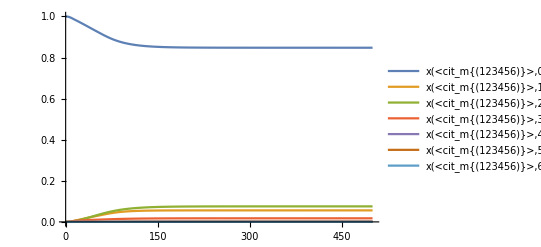

```mathematica
Block[{k=9,ix,fl,vl},
ix=Position[variables,x[EMU[Metabolite["cit","Mitochondria",_],{{Range[6]}}],_]];
fl=Extract[sol⟦k⟧,ix];
vl=Extract[variables,ix];
Plot[
Evaluate[Table[Tooltip[fl⟦i⟧[t],vl⟦i⟧],{i,Length[ix]}]],
{t,0,500},PlotRange->{0,1},PlotLegends->vl]]
```

#### Lactate

MID

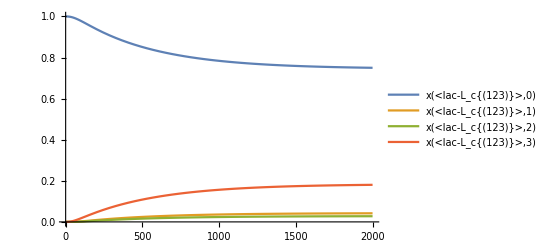

```mathematica
Block[{k=9,ix,fl,vl},
ix=Position[variables,x[EMU[Metabolite["lac-L","Cytosol",_],{{Range[3]}}],_]];
fl=Extract[sol⟦k⟧,ix];
vl=Extract[variables,ix];
Plot[
Evaluate[Table[Tooltip[fl⟦i⟧[t],vl⟦i⟧],{i,Length[ix]}]],
{t,0,tFinal},PlotRange->{0,1},PlotLegends->vl]]
```

### Compare with steady state solution

```mathematica
emuIndex=Table[Position[variables,x[e,_]],{e,targets}];
```

```mathematica
Length[emuIndex]
```

404

```mathematica
With[{k=26,t=1000},
statMIDs=Table[emuSol⟦k⟧[e],{e,targets}];
nonStatMIDs=Table[f[t],{ix,emuIndex},{f,Extract[sol⟦k⟧,ix]}]];
```

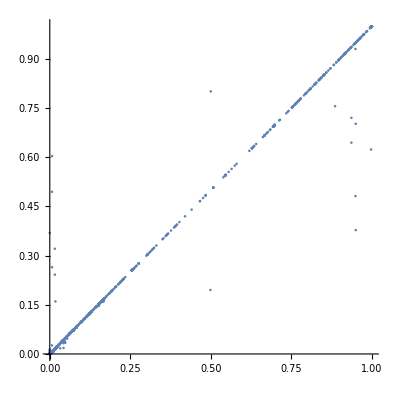

```mathematica
ListPlot[
Transpose[Flatten/@{statMIDs,nonStatMIDs}],
PlotRange->{{0,1},{0,1}},AspectRatio->1]
```

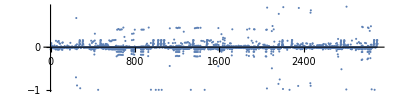

```mathematica
ListPlot[
Flatten[statMIDs]-Flatten[nonStatMIDs],
PlotRange->{All,All},AspectRatio->1/4]
```

### Export single simulation, all time points

```mathematica
timePoints={50,75,100,200,2000};
```

```mathematica
samples=Block[{k=9,functions},
functions=Extract[sol⟦k⟧,Join@@emuIndex];
Table[f[t],{t,timePoints},{f,functions}]];
```

```mathematica
Dimensions[samples]
```

{5,3097}

```mathematica
Export[
FileNameJoin[{resultDirectory,"deep-labeling.tsv"}],
Block[{mi,met},
met=Flatten[Table[MetaboliteShortName[Metabolite[e]],{e,targets},{i,0,EMUSize[e]}]];
mi=Flatten[Table[Range[0,EMUSize[e]],{e,targets}]];
ArrayFlatten[
{{{{"Metabolite","MI"}},{timePoints}},
{Transpose[{met,mi}],Transpose[samples]}}]]]
```

C:\Users\rolnil\OneDrive - KI.SE\Lab common\projects\reverse-engineering-deniz\reverse-engineering\Data\simulation\large-model\deep-labeling.tsv

## Sample all simulations

### Sample time points

```mathematica
timePoints={50,75,100,200,2000};
```

This yields a simulation x timepoint x MI array

```mathematica
samples=Block[{functions},
Table[
If[k==8,
Table[0,{t,timePoints},Total[EMUSize/@targets+1]],
functions=Extract[sol⟦k⟧,Join@@emuIndex];
Table[f[t],{t,timePoints},{f,functions}]],
{k,Length[simulationNames]}]];
```

```mathematica
Dimensions[samples]
```

{27,5,3097}

Save as MI data sets

```mathematica
NonstationaryFileName[t_]:=
FileNameJoin[{resultDirectory,"nonstationary_t"<>ToString[t]<>".tsv"}]
```

```mathematica
NonstationaryFileName[50]
```

C:\Users\rolnil\OneDrive - KI.SE\Lab common\projects\reverse-engineering-deniz\reverse-engineering\Data\simulation\large-model\nonstationary_t50.tsv

```mathematica
Do[
Export[
NonstationaryFileName[timePoints⟦k⟧],
Block[{mi,met},
met=Flatten[Table[MetaboliteShortName[Metabolite[e]],{e,targets},{i,0,EMUSize[e]}]];
mi=Flatten[Table[Range[0,EMUSize[e]],{e,targets}]];
ArrayFlatten[
{{{{"Metabolite","MI"}},{simulationNames}},
{Transpose[{met,mi}],Transpose[samples⟦All,k⟧]}}]]],
{k,Length[timePoints]}]
```